```mathematica
MakeVar[k_]:=Symbol["x"<>ToString[k]]
```

```mathematica
MyColors=Association[];
```

```mathematica
MyColors[Greater]=Green;MyColors[GreaterEqual]=Orange;MyColors[Equal]=Red
```

RGBColor[1, 0, 0]

```mathematica
edges=Flatten[Table[
Table[
{MakeVar[k]->MakeVar[child[[1]]],MakeVar[k]->MakeVar[child[[2]]]}
,{child, allGraphs4[k,"children"]}
]
,{k,Keys[allGraphs4]}]]//DeleteDuplicates
```

{x0→x243,x0→x486,x0→x81,x0→x162,x0→x27,x0→x54,x0→x9,x0→x18,x0→x3,x0→x6,x0→x1,x0→x2,x243→x324,x243→x414,x243→x270,x243→x300,x243→x252,x243→x342,x243→x246,x243→x276,x243→x244,x243→x245,x324→x351,x324→x382,x324→x333,x324→x342,x324→x327,x324→x357,x324→x325,x324→x353,x351→x360,x351→x369,x351→x354,x351→x357,x351→x352,x351→x353,x360→x363,x360→x367,x360→x361,x360→x365,x363→x364,x363→x365,x361→x364,x361→x367,x369→x373,x369→x377,x354→x363,x354→x373,x354→x355,x354→x365,x355→x364,x355→x373,x357→x367,x357→x377,x352→x361,x352→x373,x352→x355,x352→x367,x353→x365,x353→x377,x382→x391,x382→x400,x333→x360,x333→x391,x333→x336,x333→x367,x333→x334,x333→x365,x336→x363,x336→x391,x336→x337,x336→x365,x337→x364,x337→x391,x334→x361,x334→x391,x334→x337,x334→x367,x342→x369,x342→x400,x342→x346,x342→x377,x346→x373,x346→x400,x327→x354,x327→x382,x327→x336,x327→x346,x327→x328,x327→x365,x328→x355,x328→x382,x328→x337,x328→x346,x325→x352,x325→x382,x325→x334,x325→x346,x325→x328,x325→x367,x414→x442,x414→x473,x414→x417,x414→x448,x442→x445,x442→x448,x417→x445,x417→x473,x270→x351,x270→x442,x270→x279,x270→x369,x270→x273,x270→x276,x270→x271,x270→x353,x279→x360,x279→x442,x279→x282,x279→x286,x279→x280,x279→x365,x282→x363,x282→x445,x282→x283,x282→x365,x283→x364,x283→x445,x286→x367,x286→x448,x280→x361,x280→x442,x280→x283,x280→x286,x273→x354,x273→x445,x273→x282,x273→x373,x273→x274,x273→x365,x274→x355,x274→x445,x274→x283,x274→x373,x276→x357,x276→x448,x276→x286,x276→x377,x271→x352,x271→x442,x271→x280,x271→x373,x271→x274,x271→x286,x300→x382,x300→x473,x300→x309,x300→x400,x309→x391,x309→x473,x252→x333,x252→x414,x252→x279,x252→x309,x252→x255,x252→x286,x252→x253,x252→x257,x255→x336,x255→x417,x255→x282,x255→x309,x255→x256,x255→x257,x256→x337,x256→x445,x256→x283,x256→x391,x257→x365,x257→x473,x253→x334,x253→x442,x253→x280,x253→x391,x253→x256,x253→x286,x246→x327,x246→x417,x246→x273,x246→x300,x246→x255,x246→x346,x246→x247,x246→x257,x247→x328,x247→x445,x247→x274,x247→x382,x247→x256,x247→x346,x244→x325,x244→x442,x244→x271,x244→x382,x244→x253,x244→x346,x244→x247,x244→x286,x245→x353,x245→x473,x245→x257,x245→x377,x486→x576,x486→x666,x486→x516,x486→x546,x486→x487,x486→x488,x576→x606,x576→x637,x576→x577,x576→x608,x606→x607,x606→x608,x577→x607,x577→x637,x666→x697,x666→x728,x516→x606,x516→x697,x516→x517,x516→x608,x517→x607,x517→x697,x546→x637,x546→x728,x487→x577,x487→x697,x487→x517,x487→x637,x488→x608,x488→x728,x81→x324,x81→x576,x81→x108,x81→x136,x81→x90,x81→x342,x81→x84,x81→x87,x81→x82,x81→x110,x108→x351,x108→x606,x108→x117,x108→x369,x108→x111,x108→x357,x108→x109,x108→x110,x117→x360,x117→x606,x117→x120,x117→x367,x117→x118,x117→x122,x120→x363,x120→x606,x120→x121,x120→x122,x121→x364,x121→x607,x122→x365,x122→x608,x118→x361,x118→x607,x118→x121,x118→x367,x111→x354,x111→x606,x111→x120,x111→x373,x111→x112,x111→x122,x112→x355,x112→x607,x112→x121,x112→x373,x109→x352,x109→x607,x109→x118,x109→x373,x109→x112,x109→x367,x110→x353,x110→x608,x110→x122,x110→x377,x136→x382,x136→x637,x136→x145,x136→x400,x145→x391,x145→x637,x90→x333,x90→x576,x90→x117,x90→x145,x90→x93,x90→x97,x90→x91,x90→x122,x93→x336,x93→x606,x93→x120,x93→x391,x93→x94,x93→x122,x94→x337,x94→x607,x94→x121,x94→x391,x97→x367,x97→x637,x91→x334,x91→x577,x91→x118,x91→x145,x91→x94,x91→x97,x84→x327,x84→x606,x84→x111,x84→x382,x84→x93,x84→x346,x84→x85,x84→x122,x85→x328,x85→x607,x85→x112,x85→x382,x85→x94,x85→x346,x87→x357,x87→x637,x87→x97,x87→x377,x82→x325,x82→x577,x82→x109,x82→x136,x82→x91,x82→x346,x82→x85,x82→x97,x162→x414,x162→x666,x162→x190,x162→x218,x162→x165,x162→x168,x190→x442,x190→x697,x190→x193,x190→x448,x193→x445,x193→x697,x218→x473,x218→x728,x165→x417,x165→x697,x165→x193,x165→x473,x168→x448,x168→x728,x27→x270,x27→x516,x27→x108,x27→x190,x27→x36,x27→x45,x27→x30,x27→x276,x27→x28,x27→x110,x36→x279,x36→x606,x36→x117,x36→x442,x36→x39,x36→x286,x36→x37,x36→x122,x39→x282,x39→x606,x39→x120,x39→x445,x39→x40,x39→x122,x40→x283,x40→x607,x40→x121,x40→x445,x37→x280,x37→x607,x37→x118,x37→x442,x37→x40,x37→x286,x45→x369,x45→x697,x45→x49,x45→x377,x49→x373,x49→x697,x30→x273,x30→x516,x30→x111,x30→x193,x30→x39,x30→x49,x30→x31,x30→x122,x31→x274,x31→x517,x31→x112,x31→x193,x31→x40,x31→x49,x28→x271,x28→x517,x28→x109,x28→x190,x28→x37,x28→x49,x28→x31,x28→x286,x54→x300,x54→x546,x54→x136,x54→x218,x54→x63,x54→x72,x63→x309,x63→x637,x63→x145,x63→x473,x72→x400,x72→x728,x9→x252,x9→x576,x9→x90,x9→x414,x9→x36,x9→x63,x9→x12,x9→x16,x9→x10,x9→x14,x12→x255,x12→x606,x12→x93,x12→x417,x12→x39,x12→x309,x12→x13,x12→x14,x13→x256,x13→x607,x13→x94,x13→x445,x13→x40,x13→x391,x14→x257,x14→x608,x14→x122,x14→x473,x16→x286,x16→x637,x16→x97,x16→x448,x10→x253,x10→x577,x10→x91,x10→x442,x10→x37,x10→x145,x10→x13,x10→x16,x18→x342,x18→x666,x18→x45,x18→x72,x18→x22,x18→x26,x22→x346,x22→x697,x22→x49,x22→x400,x26→x377,x26→x728,x3→x246,x3→x516,x3→x84,x3→x165,x3→x30,x3→x300,x3→x12,x3→x22,x3→x4,x3→x14,x4→x247,x4→x517,x4→x85,x4→x193,x4→x31,x4→x382,x4→x13,x4→x22,x6→x276,x6→x546,x6→x87,x6→x168,x6→x16,x6→x26,x1→x244,x1→x487,x1→x82,x1→x190,x1→x28,x1→x136,x1→x10,x1→x22,x1→x4,x1→x16,x2→x245,x2→x488,x2→x110,x2→x218,x2→x14,x2→x26}

```mathematica
vertices=Table[
MakeVar[k]->MyColors[allGraphs4[k,"comp"]]
,{k,Keys[allGraphs4]}]
```

{x0→RGBColor[0, 1, 0],x243→RGBColor[0, 1, 0],x324→RGBColor[0, 1, 0],x351→RGBColor[0, 1, 0],x360→RGBColor[0, 1, 0],x363→RGBColor[0, 1, 0],x364→RGBColor[1, 0.5, 0],x365→RGBColor[0, 1, 0],x367→RGBColor[1, 0.5, 0],x361→RGBColor[0, 1, 0],x369→RGBColor[0, 1, 0],x373→RGBColor[0, 1, 0],x377→RGBColor[0, 1, 0],x354→RGBColor[0, 1, 0],x355→RGBColor[0, 1, 0],x357→RGBColor[0, 1, 0],x352→RGBColor[0, 1, 0],x353→RGBColor[0, 1, 0],x382→RGBColor[0, 1, 0],x391→RGBColor[0, 1, 0],x400→RGBColor[0, 1, 0],x333→RGBColor[0, 1, 0],x336→RGBColor[0, 1, 0],x337→RGBColor[0, 1, 0],x334→RGBColor[0, 1, 0],x342→RGBColor[0, 1, 0],x346→RGBColor[0, 1, 0],x327→RGBColor[0, 1, 0],x328→RGBColor[0, 1, 0],x325→RGBColor[0, 1, 0],x414→RGBColor[0, 1, 0],x442→RGBColor[0, 1, 0],x445→RGBColor[1, 0.5, 0],x448→RGBColor[1, 0.5, 0],x473→RGBColor[0, 1, 0],x417→RGBColor[0, 1, 0],x270→RGBColor[0, 1, 0],x279→RGBColor[0, 1, 0],x282→RGBColor[0, 1, 0],x283→RGBColor[0, 1, 0],x286→RGBColor[0, 1, 0],x280→RGBColor[0, 1, 0],x273→RGBColor[0, 1, 0],x274→RGBColor[0, 1, 0],x276→RGBColor[0, 1, 0],x271→RGBColor[0, 1, 0],x300→RGBColor[0, 1, 0],x309→RGBColor[0, 1, 0],x252→RGBColor[0, 1, 0],x255→RGBColor[0, 1, 0],x256→RGBColor[0, 1, 0],x257→RGBColor[0, 1, 0],x253→RGBColor[0, 1, 0],x246→RGBColor[0, 1, 0],x247→RGBColor[0, 1, 0],x244→RGBColor[0, 1, 0],x245→RGBColor[0, 1, 0],x486→RGBColor[0, 1, 0],x576→RGBColor[0, 1, 0],x606→RGBColor[0, 1, 0],x607→RGBColor[0, 1, 0],x608→RGBColor[0, 1, 0],x637→RGBColor[0, 1, 0],x577→RGBColor[0, 1, 0],x666→RGBColor[0, 1, 0],x697→RGBColor[0, 1, 0],x728→RGBColor[0, 1, 0],x516→RGBColor[0, 1, 0],x517→RGBColor[0, 1, 0],x546→RGBColor[0, 1, 0],x487→RGBColor[0, 1, 0],x488→RGBColor[0, 1, 0],x81→RGBColor[0, 1, 0],x108→RGBColor[0, 1, 0],x117→RGBColor[0, 1, 0],x120→RGBColor[0, 1, 0],x121→RGBColor[0, 1, 0],x122→RGBColor[0, 1, 0],x118→RGBColor[0, 1, 0],x111→RGBColor[0, 1, 0],x112→RGBColor[0, 1, 0],x109→RGBColor[0, 1, 0],x110→RGBColor[0, 1, 0],x136→RGBColor[0, 1, 0],x145→RGBColor[0, 1, 0],x90→RGBColor[0, 1, 0],x93→RGBColor[0, 1, 0],x94→RGBColor[0, 1, 0],x97→RGBColor[0, 1, 0],x91→RGBColor[0, 1, 0],x84→RGBColor[0, 1, 0],x85→RGBColor[0, 1, 0],x87→RGBColor[0, 1, 0],x82→RGBColor[0, 1, 0],x162→RGBColor[0, 1, 0],x190→RGBColor[0, 1, 0],x193→RGBColor[0, 1, 0],x218→RGBColor[0, 1, 0],x165→RGBColor[0, 1, 0],x168→RGBColor[0, 1, 0],x27→RGBColor[0, 1, 0],x36→RGBColor[0, 1, 0],x39→RGBColor[0, 1, 0],x40→RGBColor[0, 1, 0],x37→RGBColor[0, 1, 0],x45→RGBColor[0, 1, 0],x49→RGBColor[0, 1, 0],x30→RGBColor[0, 1, 0],x31→RGBColor[0, 1, 0],x28→RGBColor[0, 1, 0],x54→RGBColor[0, 1, 0],x63→RGBColor[0, 1, 0],x72→RGBColor[0, 1, 0],x9→RGBColor[0, 1, 0],x12→RGBColor[0, 1, 0],x13→RGBColor[0, 1, 0],x14→RGBColor[0, 1, 0],x16→RGBColor[0, 1, 0],x10→RGBColor[0, 1, 0],x18→RGBColor[0, 1, 0],x22→RGBColor[0, 1, 0],x26→RGBColor[0, 1, 0],x3→RGBColor[0, 1, 0],x4→RGBColor[0, 1, 0],x6→RGBColor[0, 1, 0],x1→RGBColor[0, 1, 0],x2→RGBColor[0, 1, 0]}

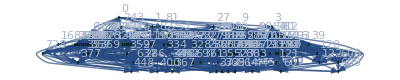

```mathematica
Graph[edges, VertexStyle->vertices, VertexLabels->Table[MakeVar[k]->Tooltip[k,allGraphs4[k,"graph"]],{k,Keys[allGraphs4]}], GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
GraphDiameter[%]
```

∞